Plots of transmission magnitude and phase for a one dimensional photonic crystal.
Plots assume: μ_1 = μ_2= 1, normal incidence, and use the Fresnel reflection coefficient ρ_ij for the TE mode polarization.

## ece1228 problem set 9, problem 2 (2016)

```mathematica
ClearAll[ mu1, mu2, n1, n2, rho, d1, d2, c, g, ej, ej, a, b, acap, bcap, m, display, phii, phij]
mu1 = 1;
mu2 = 2;
n1 = 1 ;
n2 = 3.4 - 0.002 I ;
rho = (n1 - n2)/(n1 + n2);
d1 = 1.76 10^(-2) ;  (*meters*)
d2 = 1.33 10^(-2) ;  (*meters*)
c = 2.998×10^8 ; (* meters/second*)
(*phi[omega] = -beta d = -(omega/c) n cos(theta) ; theta = 0. *)
phii = -# n1/c &;
phij = -# n2/c &;
g = 1/(1 - rho^2);
ej = Exp[I phij[#]]&;
ei = Exp[I phii[#]] &;
a = (ej[#] -rho^2/ej[#]) ei[#] &;
acap = ((1/ej[#]) - ej[#] rho^2)/ei[#] & ;
b = -rho(ej[#] - 1/ej[#])/ei[#] & ;
bcap = rho(ej[#] - 1/ej[#]) ei[#] &;
m = g {{a[#], b[#]}, {bcap[#], acap[#]}}&;
display = {psi -> ψ, omega ->ω,I -> j, -I -> -j };
(*(SetPrecision[m[ω],3] /. display)// MatrixForm *)
```

No need to explicitly calculate the eigensystem for the matrix.  The MatrixPower function is doing that anyways.

```mathematica
ClearAll[out, psi]
psi = 1; (*set equal to one so that it doesn't have to be cancelled out.  Mathematica is deferring that simplification, and it messes up the plots, making them show zero since the plot expressions contain symbols. *)
out = {0,psi ei[#]} &;
(*out[omega] /. display // MatrixForm*)
```

```mathematica
ClearAll[x, r, t, ghz]
x[omega_, n_] := MatrixPower[m[omega],n]. out[omega]  // FullSimplify;
(*SetPrecision[x[omega, 3],3] /. display // MatrixForm*)

r[omega_, n_] := (x[omega,n][[1]])/(x[omega, n][[2]]) ;
t[omega_, n_] := psi/(x[omega, n][[2]]) ;
```

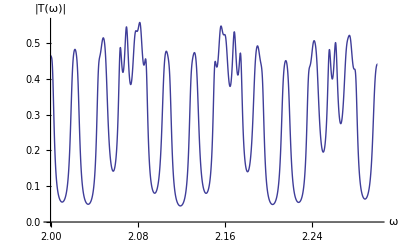

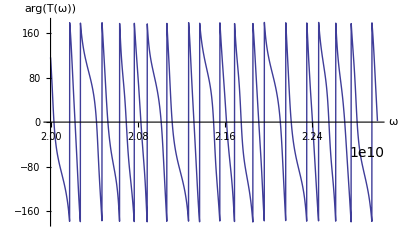

```mathematica
(*t[omega, 3] /. display
r[omega, 3] /. display *)
ghz = 10^9 ; (*1/sec*)
Plot[Abs[t[omega, 3]], {omega, 20 ghz, 23 ghz}, AxesLabel->{ω, "|T(ω)|"}]
Plot[Arg[t[omega, 3]] 180/Pi, {omega, 20 ghz, 23 ghz},AxesLabel->{ω, "arg(T(ω))"}]
```